# Deep Graph Draw

IDEA!!! 
Test walks via LSTM 
character encode vertices  and pass those characters a list for the walk (along edges)

e.g. 1->2->3
might be “ABC”

```mathematica
SimpleGraphQ
```

```mathematica
Quit[]
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
<<DeepGraphDraw`
```

```mathematica
MakeSimpleQDataset[100][All,"Output"]//Normal//Tally
```

{{True,100},{False,100}}

```mathematica
SimpleGraphQ/@AdjacencyGraph/@{{{0,1},{0,1}}}
```

{False}

```mathematica
Names["*GraphQ"]
```

```mathematica
GraphTypes=ToExpression/@{"AcyclicGraphQ","BipartiteGraphQ","CompleteGraphQ","ConnectedGraphQ","DirectedGraphQ","EmptyGraphQ","EulerianGraphQ","GraphQ","HamiltonianGraphQ","IsomorphicGraphQ","LoopFreeGraphQ","MixedGraphQ","PathGraphQ","PlanarGraphQ","SimpleGraphQ","TreeGraphQ","UndirectedGraphQ","WeaklyConnectedGraphQ","WeightedGraphQ"};
```

```mathematica
Tally[#]&@Values[#]&/@GroupBy[Flatten[(Table[ToString[t]->t@#,{t,GraphTypes}])&/@Normal[ds[All,"Input"]]],First]
```

<|AcyclicGraphQ→{{False,20000}},BipartiteGraphQ→{{True,20000}},CompleteGraphQ→{{False,20000}},ConnectedGraphQ→{{False,20000}},DirectedGraphQ→{{False,20000}},EmptyGraphQ→{{False,20000}},EulerianGraphQ→{{False,20000}},GraphQ→{{False,20000}},HamiltonianGraphQ→{{False,20000}},IsomorphicGraphQ→{{False,20000}},LoopFreeGraphQ→{{False,20000}},MixedGraphQ→{{False,20000}},PathGraphQ→{{False,20000}},PlanarGraphQ→{{False,20000}},SimpleGraphQ→{{False,20000}},TreeGraphQ→{{False,20000}},UndirectedGraphQ→{{False,20000}},WeaklyConnectedGraphQ→{{False,20000}},WeightedGraphQ→{{False,20000}}|>

```mathematica
Length@ds
```

20000

```mathematica
ds=MakeDataset[20000, 
"NumberOfVertices"->10,
"ProbabilityOfEdge"->0.5,
"GraphLayout"->"LayeredEmbedding",
"DiscretizeCoordinates"->False];
pd=PartitionData[ds, {0.7, 0.2, .1}];
```

```mathematica
Tally@(SimpleGraphQ/@AdjacencyGraph/@Normal[ds[All,"Input"]])
```

{{True,5000}}

```mathematica
SimpleGraphQ@AdjacencyGraph@{{1,1},{0,0}}
```

False

```mathematica
RandomG
```

```mathematica
(*PlanarGraphQ, AcyclicGraphQ, SimpleGraphQ, MultigraphQ *)
```

## Look at generated data

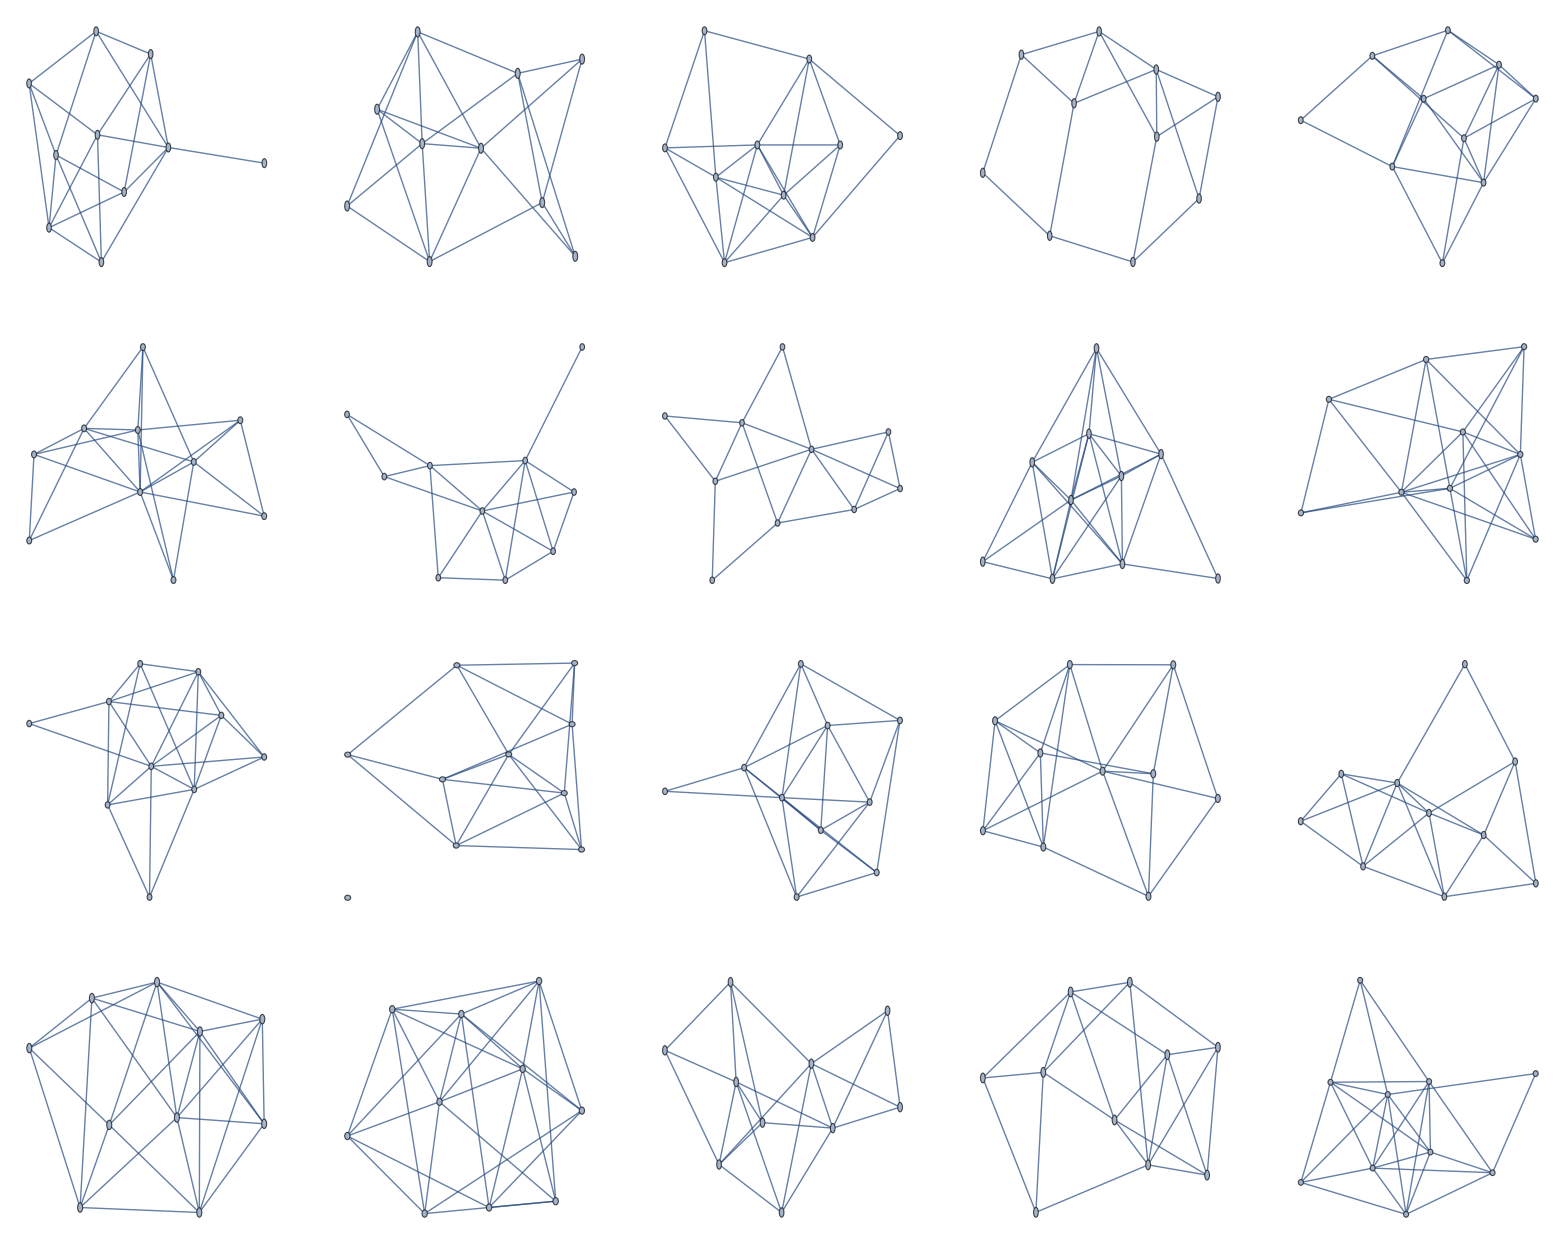

```mathematica
GraphicsGrid[Partition[AdjacencyGraph/@Normal[ds[All,"Input"][[1;;20]]],{5}]]
```

#### How to compare Input with Output

```mathematica
CompareForcedCoordinates[
Normal[#["Input"]],
 Normal[#["Output"]],
"PrintReadyQ"->True,
"GraphLayout"->"LayeredEmbedding" (* only effects the original graph's drawing *)
]&@ds[[1]]
```

## Make Net

```mathematica
net=NetInitialize@NetChain[
{
ConvolutionLayer[128,{3}, "PaddingSize"->1],
Tanh,
ConvolutionLayer[256,{3}, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[512,{3}, "PaddingSize"->1],
Tanh,
ConvolutionLayer[1024,{3}, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[2048,{3}, "PaddingSize"->1],
Tanh,
ConvolutionLayer[1024,{3}, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[512,{3}, "PaddingSize"->1],
Tanh,
ConvolutionLayer[256,{3}, "PaddingSize"->1],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[128,{3}],
Tanh,
ConvolutionLayer[64,{3}],
Ramp,
BatchNormalizationLayer[],
ConvolutionLayer[32,{3}],
Tanh,
ConvolutionLayer[10,{3}],
Tanh
},
"Input"-> inputDimension(*,
"Output"-> {First[inputDimension],2}*)
]
```

NetChain[<>]

```mathematica
inputDimension=Dimensions[First[First[ds]]];
```

```mathematica
net=NetInitialize[
NetChain[
{
LinearLayer[inputDimension],
LinearLayer[First[inputDimension]^2],
Tanh,
LinearLayer[First[inputDimension]^3],
Ramp,
LinearLayer[First[inputDimension]^3*4],
Tanh,
LinearLayer[First[inputDimension]^3*8],
Ramp,
LinearLayer[First[inputDimension]^3],
Tanh,
LinearLayer[{First[inputDimension],2}]
},
"Input"-> inputDimension
]
];
```

```mathematica
tnet=NetTrain[net,pd["TrainingData"],ValidationSet->pd["ValidationData"],TargetDevice->"CPU"];
```

```mathematica
Export[NotebookDirectory[]<>"dgd_test.wlnet",tnet]
```

/Users/sumner/Programming/WSS2018/DeepGraphDraw/dgd_test.wlnet

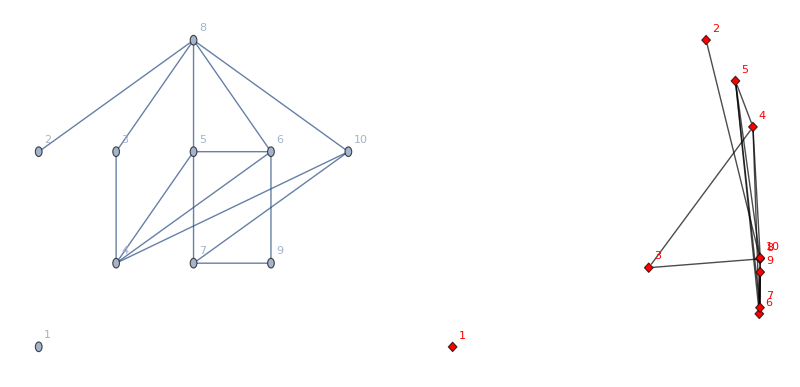
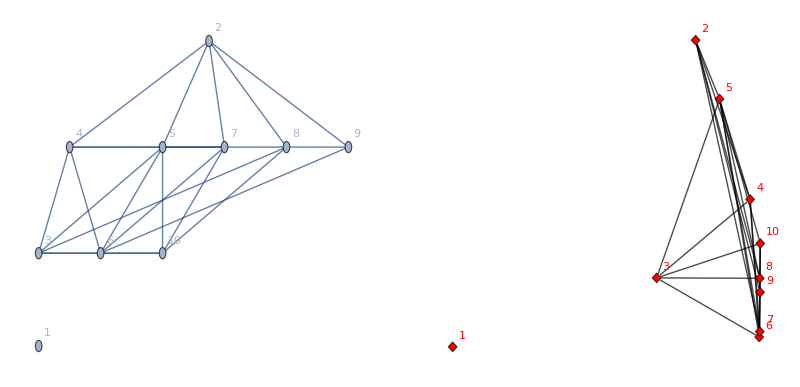
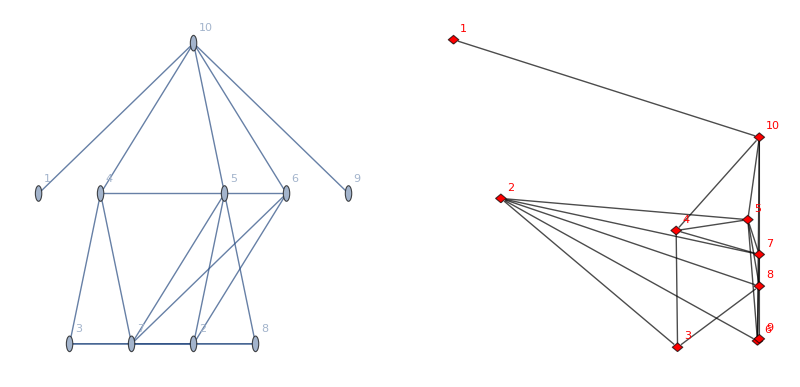
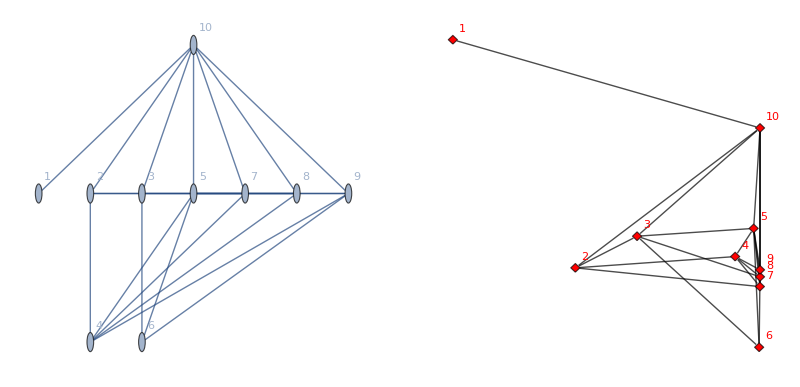
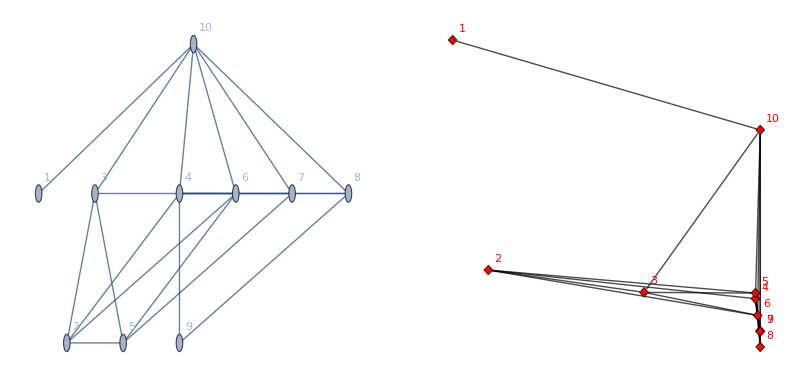
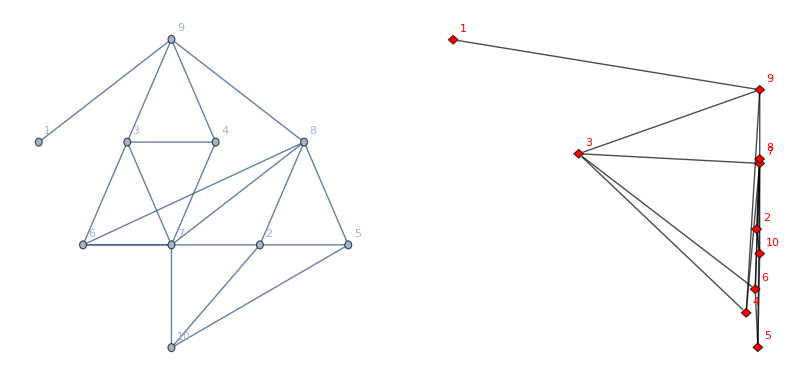
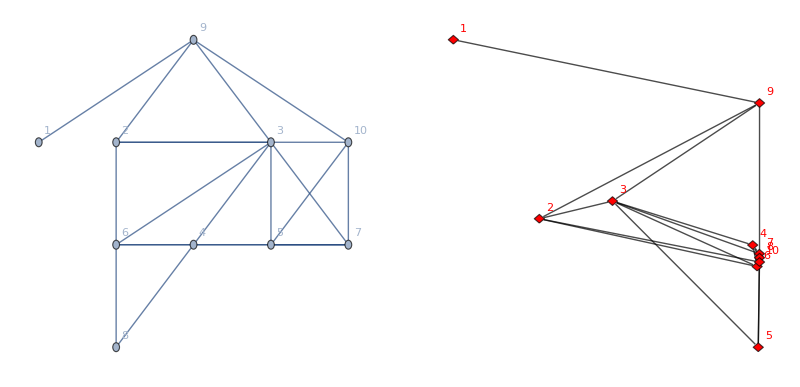
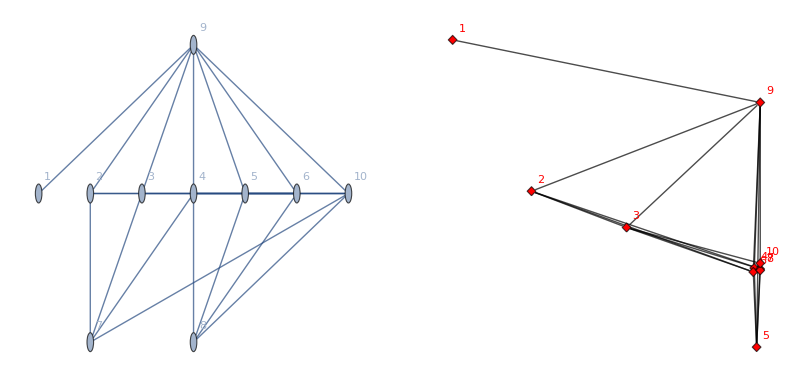

```mathematica
CompareForcedCoordinates[
#[[1]],
 #[[2]],
"PrintReadyQ"->True,
"GraphLayout"->"LayeredEmbedding" (* only effects the original graph's drawing *)
]&/@
Partition[Riffle[
Normal[pd["TestData"][1;;20,"Input"]],
 tnet[Normal[pd["TestData"][1;;20,"Input"]]]
],{2}]
```

## Use results

```mathematica
wnet=Import@"~/Desktop/graph_results/gec2/results/graph_net.wlnet";
gds=Import@"~/Desktop/graph_results/gec2/graph_dataset.mx";
```

```mathematica
Length@gds
```

100000

```mathematica
wnet
```

NetChain[<>]

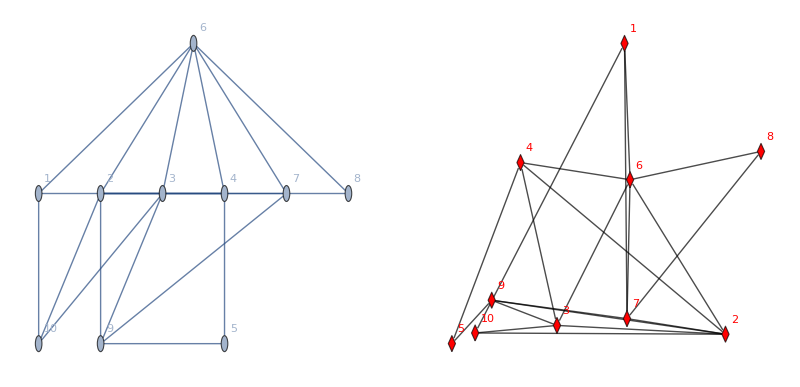
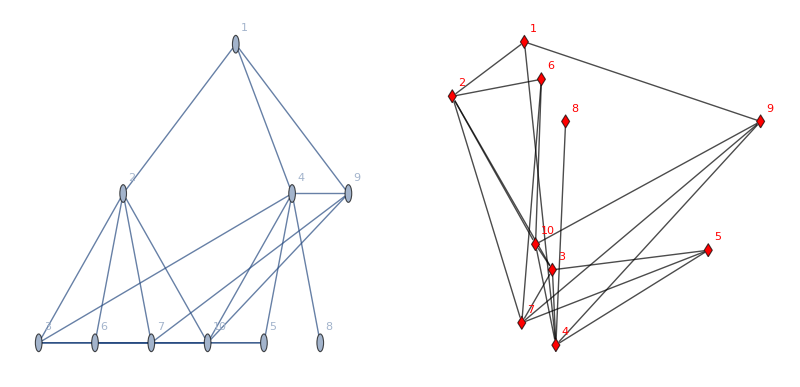
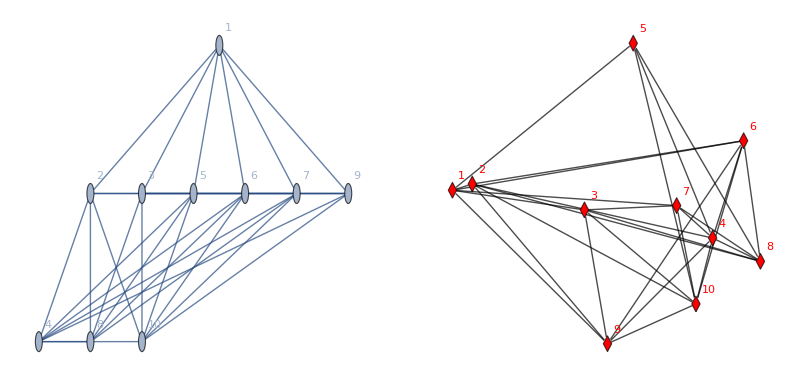
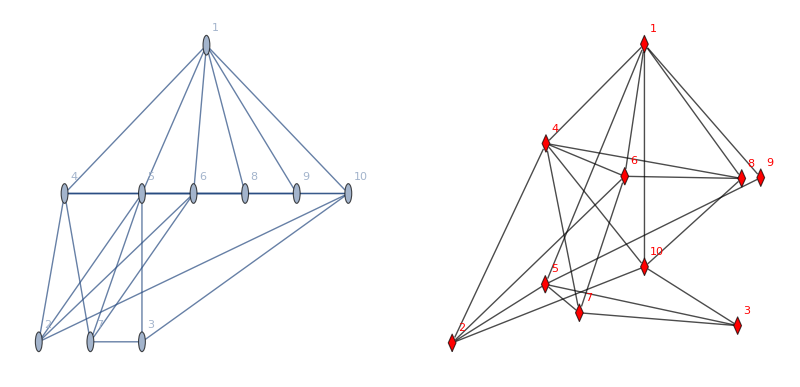
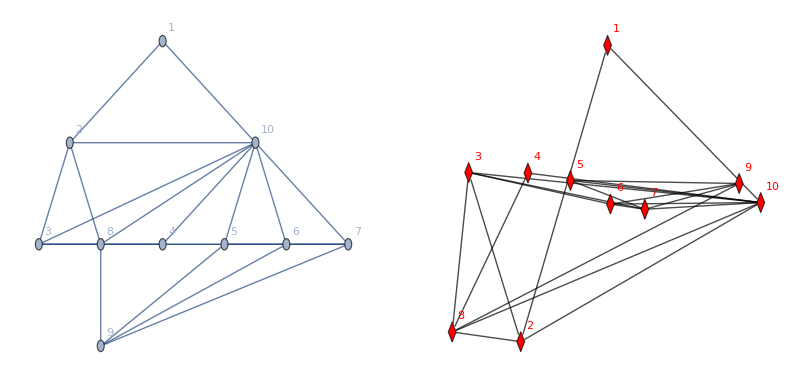
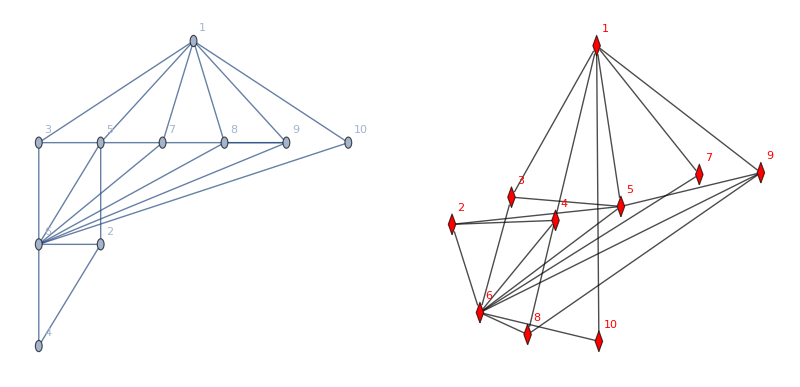
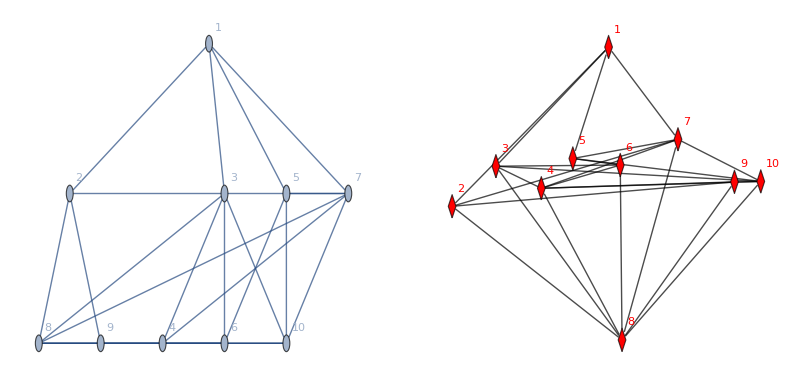
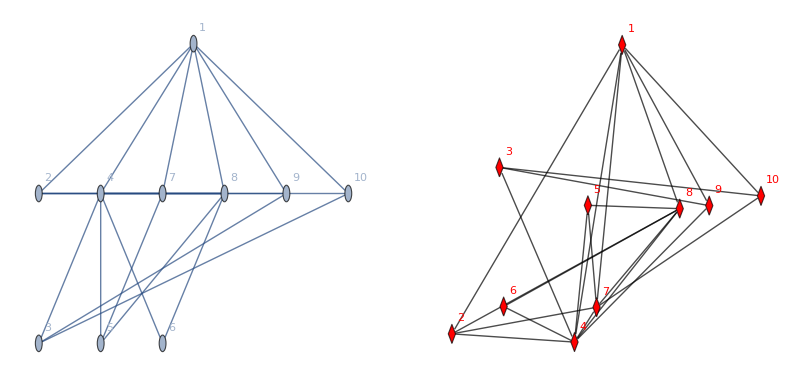

```mathematica
CompareForcedCoordinates[
#[[1]],
 #[[2]],
"PrintReadyQ"->True,
"GraphLayout"->"LayeredEmbedding" (* only effects the original graph's drawing *)
]&/@
Partition[Riffle[
Normal[RandomSample[gds,20][All,"Input"]],
 wnet[Normal[RandomSample[gds,20][All,"Input"]]]
],{2}]
```

```mathematica
SimpleGraphQ@AdjacencyGraph[{{0,1},{1,1}}]
```

False

$Aborted